# (Monte-Carlo) Positron-Emission- Entanglement Tracking Simulation (MC P.E.E.T.S)

Nathan Ngqwebo

University of Cape Town

```mathematica
Clear["Global`*"];
(*Quit[];*)
```

## Cross sections

Some Constants:

```mathematica
electronRadius=2.8179403227*10^-13 ; (*electron radius in cm*)
electronMass=9.10938×10^-28; (*electron mass in grams*)
r=1; (*can do this because σKN is only used for the (dimensionless) scattering angle. Moreover, we only need the distribution*)
ρ=5.76; (*g/cm^3 CdZnTe mass density: Detector material*)
$Assumptions γ >0;
```

Klein-Nishina

From the Klein-Nishina cross-section for Compton interactions, we have the differential cross-section describing the proportion of γ-rays scattered off a small crossection dσ into a solid angle dΩ.
SIMPLIFICATION: x = cos(θ)

```mathematica
dσdΩ[x_, γ_] = r^2/2(1+x^2+(γ^2(1-x)^2)/(1+ γ (1-x)))/(1+γ (1-x))^2;(*Almost a valid PDF. Just needs normalisation*)
```

Here, we find the area under the differential cross-section to give us our normalisation constant σ_KN.

```mathematica
(*rawCDF[X_, γ_] = Integrate[dσdΩ[x,γ],{x,-1,X}, {ϕ, 0, 2Pi},Assumptions->{γ>0, -1<X ≤ 1}]//Simplify;*)
```

```mathematica
σKN[γ_]= 2π Integrate[dσdΩ[x,γ],{x,-1,1},Assumptions->{γ>0, -1<=x<=1}]//FullSimplify;
```

Now, we can have a valid PDF for the scattering angle θ -i.e., θ.

```mathematica
pKN[x_, γ_]=(2Pi dσdΩ[x,γ])/σKN[γ] ;
(*2Pi factor from integrating out the ϕ dependence of pKN and leaving a marginal PDF in x and γ*)
```

CDF at the endpoint = 1 ?

```mathematica
Integrate[pKN[x,γ],x];
cdfKN[x_,γ_]=%-(%/.x->-1)//FullSimplify;
(*Using definition from A.P because of edge case where cdfKN is undefined at x=-1*)
(*Manipulate[Plot[cdfKN[x, γ],{x,-1,1},AxesLabel->{"x=Cos(θ)", "CDF_KN(x)"}, Filling->Bottom, PlotStyle->Black],{{γ, 1, "E_γ/m_e"},1*10^-3,1}]*)
```

PDF ≥ 0 ?

```mathematica
(*Manipulate[Plot[pKN[x, γ],{x,-1,1},AxesLabel->{"x=Cos(θ)", "p_KN(x)"}, Filling->Bottom, PlotStyle->Black],{{γ, 1, "E_γ/m_e"},1*10^-3,1}]*)
```

Checking against the expected value of σ_KN.

```mathematica
(*ΣKN[γ_]=2π r^2((1+γ)/γ^2 ((2(1+γ))/(1+2 γ)-Log[1+2 γ]/γ)+Log[1+2 γ]/(2 γ)-(1+3 γ)/(1+2  γ)^2)// Simplify;
N[σKN[γ]/ΣKN[γ]] //FullSimplify*)
```

Nice!

Experimental Data

```mathematica
(*Defining total crossection and Absorbtion/Compton proportions using experimental data*)
$filepath = FileNameJoin[{NotebookDirectory[], "CdZnTe_Cleaned.csv"}];
$data = Import[$filepath,"Dataset","HeaderLines"->1][All,{"photonEnergy", "photoelectricAbsorbtion", "incoherentScatter","totalNoCoherent", "totalWithCoherent"}];
$energy = $data[All, 1] //Normal;
$absorbtion = $data[All, 2]//Normal;
$compton= $data[All, 3]//Normal;
$totalcross = $data[All,4]//Normal;
$totalcrossCoh = $data[All,5]//Normal;
(*Interpolating the log data is much smoother than the raw!*)
$logσA = Interpolation[Transpose[{$energy, Log[$absorbtion]}], Method->"Hermite"];
$logσC=Interpolation[Transpose[{$energy, Log[$compton]}], Method->"Hermite"];
$logσTot  =Interpolation[Transpose[{$energy, Log[$totalcross]}], Method->"Hermite"];
$logσTotCoh  =Interpolation[Transpose[{$energy, Log[$totalcrossCoh]}], Method->"Hermite"];
(*converting back to regular crossections as pure-functions*)
σA[γ_]:=ⅇ^($logσA[γ]);
σC[γ_]:=ⅇ^($logσC[γ]);
σTot[γ_]:=ⅇ^($logσTot[γ]);
σTotCoh[γ_]:=ⅇ^($logσTotCoh[γ]);
```

```mathematica
(*modelKN[γ_]:=(-0.000180836+0.000160292  Sqrt[511 γ])/(-0.995838+Exp[0.0000829364 *511 *γ])×(electronMass/(100^2×electronRadius^2))^-1; (*Dimensions hurt my brain*)
σA[γ_] := 0.26959/γ; (*naive approach*)
modelAbs[γ_]:=Exp[(-5.89174 (1+0.347028 Log[511 γ/1000]-0.0449844 Log[511 γ/1000]^2))/(1+0.0237501 Log[511 γ/1000]^2)]  ×(electronMass/(100^2×electronRadius^2))^-1;
σINT[γ_]:=σKN[γ]+modelAbs[γ];*)
```

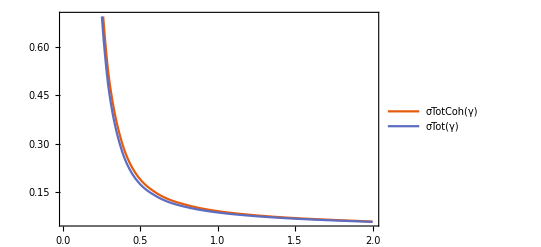

```mathematica
Plot[{σTotCoh[γ],σTot[γ] },{γ,0.02,2}, PlotLegends->"Expressions", PlotTheme->"Scientific", GridLines->{{0.02, 1/3, 2/3,1}}]
```

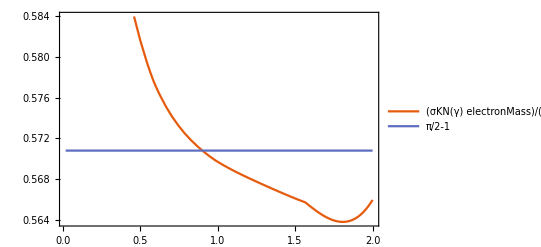

```mathematica
Plot[{σKN[γ]×(electronMass/electronRadius^2)/σC[γ], 1/2π-1},{γ,0.02,2}, PlotLegends->"Expressions", PlotTheme->"Scientific", GridLines->{{0.02, 1/3, 2/3,1}}]
```

## Beam Modelling

### Sampling

We need to sample a few values:

```mathematica
(*SeedRandom[34]*)
```

#### Sampling distance travelled through medium: s

```mathematica
λ[γ_]:=1/(ρ σTot[γ]) ;
pS[S_, γ_]:=1/λ[γ] E^(-S/λ[γ]) //Simplify;
cdfS[S_, γ_]:= 1 - ⅇ^(-S/λ[γ])
inverseCDFS[rs_, γ_]:= (-Log[rs])/(ρ σTot[γ]);
samplePathLength[γ_]:= (-Log[RandomReal[]])/(ρ σTot[γ]);
(*inverse CDF of distance through medium*)
```

Two methods available: Define new ProbabilityDistribution or just use what we have.

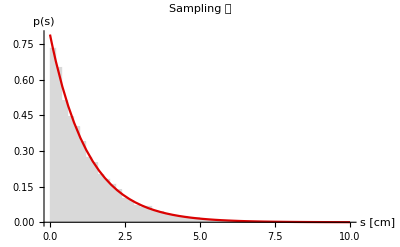

```mathematica
data=inverseCDFS[RandomReal[1, 10^4], 0.6];
(*𝒮 = ProbabilityDistribution[1/λ[1] E^(-S/λ[1]), {S, 0, ∞}] //Simplify;*)
(*data1 = RandomVariate[𝒮, 10^4]; (*Inbuilt sampling method,*)*)
Show[
Histogram[data, Automatic,"PDF",PlotLabel->"Sampling 𝓈",ChartStyle->LightGray, PlotRange->{{0, 10}, All}],
Plot[pS[S, 0.6], {S, 0, 10}, PlotStyle->2, PlotRange->Full],
AxesLabel->{Style["s [cm]", Bold, Medium], Style["p(s)", Bold, Medium]}]
```

#### Sampling Scattering angle :ϕ

```mathematica
sampleAzimScatter[]:=2π RandomReal[];
(*rϕ= RandomReal[2π, 10^4];*)
(*Show[
Histogram[rϕ,{π/10},"PDF",PlotLabel->"Sampling ϕ",ChartStyle->LightGray], 
Plot[1/(2π), {ϕ, 0, 2π}, PlotStyle->2]]*)
```

#### Sampling latitudinal scattering angle: θ [First attempt]

We only need to sample for the cases when γ ≠ 1. So we perform inverse cdf sampling on a 7^th-order Power series approximation of the cdfKN. 
We compare this method to the numerical inversion “trick” for various γ values.

```mathematica
(*seriesCDFKN[x_, γ_]= Series[cdfKN[x, γ],  {x, 0, 8}] ;
seriesInverseCDFKNRight[y_, γ_] = InverseSeries[Series[cdfKN[x, γ],  {x, 1, 5}], y];
seriesInverseCDFKNLeft[y_, γ_] = InverseSeries[Series[cdfKN[x, γ],  {x, -1, 5}], y];*)
```

```mathematica
(*xData = Subdivide[-1., 1, 10^2];
cdfData = cdfKN[xData, 1];
points = Transpose[{cdfData, xData}];
(*Cubic Spline interpolation*)
inverseCDFKN = Interpolation[points, Method->"Spline"];
Manipulate[Show[
ListPlot[Transpose[{cdfKN[xData, γ],xData  }], PlotLabel->"Left and Right Power Series Expansions of inverseCDFKN",AxesLabel->{"r_θ = p_KN(x)", "x=Cos(θ)"}, Axes->{True,True}, PlotStyle->Black], 
Plot[{Evaluate[Normal[seriesInverseCDFKNRight[r, γ] ]], Evaluate[Normal[seriesInverseCDFKNLeft[r, γ] ]]}, {r, 0, 1}, PlotLegends->"Expressions"]], {{γ, 0.33, "E_γ/m_e"}, 11/511, 1}]
*)
```

We   may   have   trouble   with   sampling   values   of   x -> 1   because   of   resolution . 
[TODO] : I   propose   splitting   the   xData   into   Left   and   Right   for   x : cdfKN[x] < 50  %   and   x : cdfKN[x] > 50  % .
and   increasing   the   number   of   points   in   xDataRight .
This   may   make   interpolation   smoother?

```mathematica
(*Histogramming the sampled data*)
(*I think Mathematica is treating the area below x = 0 as negative, thus messing up the normalisation of the histogram.*)
(*dataθ =inverseCDFKN[RandomReal[1,10^5]];
Show[
Histogram[dataθ,{-1, 1, 0.05},"PDF",PlotLabel->"Sampling θ", PlotRange->All,ChartStyle->LightGray],
Plot[pKN[x, 1], {x,-1, 1},PlotRange->All, PlotStyle->2],
AxesLabel->{"x = Cos(θ)", "p_KN(x)"}]*)
```

I may need a 3D inverseCDF: NAH!! NO NEED!
[TODO:] xData, γData meshgrid -> cdf[xv, γv] -> Invert(x=cdf reflection?) -> InverseCDF

```mathematica
(*γData = Subdivide[0.0001, 1, 10^2];
inverseCDFData=Table[(*Calculate inverse CDF data for each gamma*)xData=Subdivide[-1.,1,10^2];
cdfData=cdfKN[xData,γ];
points=Transpose[{cdfData,xData}];
Interpolation[points,Method->"Spline"],{γ,γData}]

(*Define a function to interpolate inverse CDF based on gamma*)inverseCDFInterpolated[γ_?NumericQ]:=inverseCDFData[[Nearest[γData,γ][[1]]]][γ];
(*Sample from the interpolated inverse CDF*)
dataTheta=Table[inverseCDFInterpolated[RandomChoice[γData]][RandomReal[]],{10^5}];*)
```

#### Sampling latitudinal scattering angle: θ [credit: A.P.]

```mathematica
(*set up regular grid for Subscript[ICDF, KN]*)
$γmin=0.02;$γmax=1;
$nγ=64;$nξ=64;$nr=64;
(*generate list of 1D interpolations which are slices of the Subscript[ICDF, KN] in constant  γ*)
$ξC[γ_]:=Interpolation[{cdfKN[#,γ],#}&/@ Subdivide[-1.,1,$nξ]];
$ξC[#][Subdivide[0.,1,$nr]]&/@ Subdivide[$γmin,$γmax,$nγ];
(*stitch interpolations into Subscript[ICDF, KN] surface*)
inverseCDFKN=ListInterpolation[Transpose@%,{{0,1},{$γmin,$γmax}}];
samplePolarScatter[γ_]:=inverseCDFKN[RandomReal[], γ];
```

#### updated Energy from incident energy and scattering angle

γ' = γ/(1+ γ(1-x))

```mathematica
δγ[γ_, x_]= (γ^2(1-x))/(1+ γ(1-x)); (*δγ = γ' -γ*)
```

#### Sampling Interaction type

```mathematica
interactionType[γ_]:=If[RandomReal[]<σC[γ]/σTot[γ], 1, 0]; (*1 - Compton & 0 -Absorption*)
```

#### Sampling Hit-points & Initial Photon state

Placing the source a distance z_0 away from the detector face, we will observe an incident γ-ray intensity pattern which goes as ℐ=𝒩/(x^2+y^2+z_0^2). From this we can sample hit-points on the detector face.

```mathematica
(*Define a module that initializes the inverse CDF and provides a method for sampling hit points*)
generateStateSampler[z0_,{a_,b_},{c_,d_},gridResolution_:{16,16}]:=Module[{f,𝒻,Nx,Ny,Δx,Δy,$x,$y,$𝒻,CMF,CMFindices,inverseCMF,Pair,ijPoint,X,Y},

(*Define Distribution*)
(*z0 is the source-detector separation along z-axis*)
f[x_,y_]=1/(x^2+y^2+z0^2);

(*Normalise Distribution*)
𝒻[x_,y_] = f[x,y] / NIntegrate[f[x,y],{x,a,b}, {y,c, d}];

(*Discretize PDF*)
Nx= gridResolution[[1]];
Ny = gridResolution[[2]];
Δx = (b-a)/Nx;
Δy = (d-c)/Ny;

(*Divide Domain into Nx*Ny (centered) Cells*)
$x[j_]:=a +Δx (j - 1/2);
$y[i_]:=c+Δy (i - 1/2);

(*Compute Distribution Values on the Grid*)
$𝒻=Table[𝒻[$x[j],$y[i]], {j, 1, Nx}, {i, 1, Ny}];

(*Flatten and Cumulative Sum Discretized Distribution into a CMF*)
CMF = Prepend[Accumulate[Flatten[$𝒻]×(Δx  Δy)],0];
CMFindices = Range[0, Nx Ny];

(*Numerically Invert and Interpolate the CMF*)
inverseCMF = Interpolation[Transpose[{CMF, CMFindices}]];

(*helper function: Convert Sampled Path Length to (i,j) Pair*)
Pair[ℓ_]:={Quotient[ℓ-1, Ny]+1, Mod[ℓ-1,Nx]+1};

(*Get (i,j) Pair from Uniform r ∈ [0, 1]*)
ijPoint[r_]:=Pair[Ceiling[inverseCMF[r]]];

(*Add Uniform Noise to Spread (Subscript[x, j],Subscript[y, i]) Position over Grid Cell*)
X[x_]:=x+RandomReal[{-Δx/2, Δx/2 }];
Y[y_]:= y+RandomReal[{-Δy/2, Δy/2 }];

(*function to sample full photon state*)
samplePhoton[]:=Module[{r,i,j, x, y, θ, ϕ},
r=RandomReal[];
{i, j} = ijPoint[r];
x=X[$x[j]];
y=Y[$y[i]];
θ=ArcTan[z0, Sqrt[(x^2+y^2)]];
(*θ=ArcCos[z0/Sqrt[(x^2+y^2+z0^2)]];*)
ϕ=ArcTan[x, y];
Return[
(*{{x, y, z}, {θ,ϕ}, γ, dγ}*)
{{x, y, z0}, {θ,ϕ}, 1, 0}];
];

(*(*function to sample hit point*)
sampleHitPoint[]:=Module[{r, i, j},
r=RandomReal[];
{i, j} = ijPoint[r];
Return[{X[$x[j]], Y[$y[i]]}];

];*)

(*Return the Function to Sample Full Photon State*)
samplePhoton
]
```

```mathematica
Sampling Hit-points & Initial Photon stateSampling Hit-points & Initial Photon state
```

Initial Photon state (Sampling Hit-points& Initial Photon stateSampling Hit-points&)

#### Sampling Relative azimuthal angle Δϕ [Credit: A.P.]

```mathematica
(* PDF: double-Compton scattering of entangled γ pair [Pryce1947] *)
p[x1_,x2_,φ_]=(kA[x1]kA[x2]-kB[x1]kB[x2]Cos[2φ])/π;
kB[x_]=(1-x^2)/(2-x)^2;
(* conditional PDF: p(φ|Subscript[x, 1] Subscript[x, 2]); ϕi = Subscript[k, B][Subscript[x, 1]]Subscript[k, B][Subscript[x, 2]]/(Subscript[k, A][Subscript[x, 1]]Subscript[k, A][Subscript[x, 2]]) *)
pφ=2/π-β Cos[2φ];
(* CDF of Subscript[p, φ] for given β *)
cφ[φ_,β_]=(2φ)/π-β/2 Sin[2φ];
(* to calc rnd φ from uni-rnd r for given β
 $φ0: start point for FindRoot, from lin interpol of pφ (cf appdx)
  NB: FindRoot gives value in [0,π/2], then rnd sign
 *)
$φ0[r_,β_]=π (2β+√((1-2β)^2+8β r)-1)/(8β)//Abs
©φ[r_,β_]:=RandomChoice[{-1,1}]φ/.FindRoot[cφ[φ,β]==r,{φ,$φ0[r,β]}]
```

1/8 π Abs[(-1+2 β+√((1-2 β)^2+8 β))/β]

```mathematica
sampleDeltaPhi[x1_, x2_]:=©φ[RandomReal[],(kB[x1]kB[x2])/(pKN[x1, 1]pKN[x2, 1])]
```

## Simulation

## Detector Dimensions

```mathematica
(*Cuboid Region Test Generator based on 6 plane position test*)
generateDetectorRegion[{{xlower_, xupper_}, {ylower_, yupper_}, {zlower_, zupper_}}]:=Module[{isInDetector},
isInDetector[{x_, y_, z_}]:=If[xlower <=x <= xupper && ylower <=y <= yupper && zlower <=z <= zupper, Return[True], Return[False]];
Return[isInDetector]
]

(*Energy Resolution Test Generator*)
generateEnergyResolutionLimit[γmin_]:=Module[{isγResolved},
isγResolved[γ_]:=If[γ >= γmin,Return[True], Return[False]];
Return[isγResolved]
]
```

```mathematica
a = 10; b=10; c=10; z0=10;
(*Detector Parameters*)
(*detector geometry. See sketch above*)
(*forward escape detector distance from main detector back*)
energyResolution = 0.02;
```

```mathematica
(*Initialise Detectors*)
withinDetector1 = generateDetectorRegion[{{-a,a}/2,{-b,b}/2, {0, c+z0}}];
(*isInDetector2 = generateDetectorRegion[{{-5,5},{-5,5}, {-10, -8}}];*)
isEnergyResolved = generateEnergyResolutionLimit[energyResolution]
(*Initialise State Sampler*)
samplePhotonD1 = generateStateSampler[z0, {-a, a}/2,{-b,b}/2, {16,16}]
```

isγResolved$6946

samplePhoton

## mETHODS

Particles are implemented as a list: State with:
	position{𝓍, 𝓎, 𝓏}, 
	direction{θ, ϕ} (unit vector of momentum),  
	energy{γ},

```mathematica
(*(*Cuboid Region Test*)
isInBox[{x_, y_, z_}, {xl_, xu_, yl_, yu_, zl_, zu_}]:=
If[xl <=x <= xu && yl <=y <= yu && zl <=z <= zu, 
Return[True], Return[False]];*)

(*(*Energy Resolution Test*)
isEnergyResolved[γ_, γmin_]:=
If[γ > γmin,
Return[True], Return[False]];*)

(*use my own FromSphericalCoordinates*)
fromSphericalCoords[r_, {θ_, ϕ_}]:={
r Sin[θ] Cos[ϕ], 
r Sin[θ] Sin[ϕ],
r Cos[θ]
};
```

```mathematica
(*From the inner product of spherical polar unit vectors r̂(Subscript[θ, 1], Subscript[ϕ, 1]) and r̂(Subscript[θ, 2], Subscript[ϕ, 2])*)
updatedDirection[{θi_, ϕi_}, Θ_,  Φ_]:=Module[{θ1=θi, ϕ1=ϕi, θ2, ϕ2, Δϕ, cosΔϕ1, sinΔϕ2},
θ2=ArcCos[Cos[θ1] Cos[Θ]+Sin[θ1] Sin[Θ] Cos[Φ]];
cosΔϕ1=(Cos[Θ] - Cos[θ2] Cos[θ1])/(Sin[θ1] Sin[θ2]);
sinΔϕ2=(Sin[Θ] Sin[Φ])/Sin[θ2];
(*Δϕ=ArcTan[sinΔϕ2/cosΔϕ1]; (*Does not respect sign -> quadrant of origin!!*) *)
Δϕ=ArcTan[cosΔϕ1, sinΔϕ2]; (*Thanks, David*)

{ 2π-θ2, -Δϕ+ϕ1}
];
```

```mathematica
comptonScatter[{{x0_, y0_, z0_}, {θ0_, ϕ0_},γ0_ , dγ_}]:=Module[{Φ, 𝕩, Δγ, γ=γ0, direction}, 
(* Sample Uniform Azimuthal Scattering Angle*)
Φ=sampleAzimScatter[]; 
(* Sample Polar Scattering Angle from Subscript[dσ, KN] dΩ*) (*TODO: γ<0.02 is not definde in interpolation of ICDFKN*)
𝕩=samplePolarScatter[γ0] ;
(*Update Energy Post-Scatter*)
Δγ=δγ[γ0, 𝕩]; 
(* decrement photon energy according to Compton formula*)
γ-= Δγ;
direction=updatedDirection[{θ0, ϕ0},  ArcCos[𝕩], Φ];
Return[{{x0, y0, z0},direction,γ, Δγ}]
]
```

```mathematica
(*(*To be used in NestList. This function updates the state of a particle*)
(*dummy parameter dγ so that NestWhileList will keep track of energy deposits: i didn't want to calculate them myself*)
updateState[{x0_, y0_, z0_}, {θ0_, ϕ0_},γ0_ , dγ_]:=
Module[{x = x0, y=y0, z=z0, position, θ=θ0, ϕ=ϕ0, γ=γ0, s, Φ, 𝕩, Δγ=0},
(*May need an Out of Medium check here*)
s=samplePathLength[γ0];
 position={x0, y0, z0}+ fromSphericalCoords[s, {θ0, ϕ0}]; (* update position from s and {θ0, ϕ0*)
(*Potential Savings: only update position if In-Medium Return last position In-Medium with last Direction*)
If[!isInBox[position, detectorPlanes], 
(* if Out of Medium return State Implicit Detector boundary*)
(*Echo["Out of Medium"];*)
Return[{position, {θ0, ϕ0},γ0, Δγ}];
,
If[interactionType[γ0]==0, (* if absorption or too low energy for resolution, then set energy to zero and return State*)
Δγ=γ;
γ=0;
(*Echo["Absorption"];*)
Return[{position, {θ0, ϕ0},γ, Δγ}];(*Do I need Return statements? *)
,
Φ=2π RandomReal[]; (* sample uniform azimuthal scattering angle*)
𝕩=inverseCDFKN[RandomReal[], γ0] ;(* sample polar scattering angle from Subscript[dσ, KN] dΩ*) (*TODO: γ<0.02 is not definde in interpolation of ICDFKN*)
Δγ=δγ[γ0, 𝕩];
γ-= Δγ;(* decrement photon energy according to Compton formula*)
{θ, ϕ}=updatedDirection[θ0, ϕ0,  ArcCos[𝕩], Φ];
Return[{position, {θ, ϕ},γ, Δγ}]
]; 
];
];*)
```

```mathematica
(*Function to Generate a Photon's Propagation History given a photon object and a detector boundary checker*)
propagatePhoton[photon_, withinDetector_]:=Module[{absorbed,escaped,interaction},
absorbed=False;
escaped=False;
NestWhileList[Module[{newPhoton=#},
(*Record Initial Photon State & Subsequent Beginning States*)
s = samplePathLength[newPhoton[[3]]];
newPhoton[[1]] += fromSphericalCoords[s, newPhoton[[2]]];
If[!withinDetector[newPhoton[[1]]],
escaped=True;
newPhoton[[4]]=0;
newPhoton,
(*Switch-Case for Different Interaction Types*)
interaction=interactionType[newPhoton[[3]]];
Switch[interaction,
0,
(
absorbed=True;
(*Store absorbed energy*)
newPhoton[[4]]=newPhoton[[3]];
(*Set energy to 0*)
newPhoton[[3]]=0;
newPhoton  
),
1,
(
(*Compton Scatter*)
newPhoton=comptonScatter[newPhoton];
newPhoton
),
_,
(*Default case*)
(
newPhoton
)
]
]
]&,
photon, isEnergyResolved[#[[3]]] && !absorbed &&!escaped&, 1, 27]
]
```

## Sim (Single Detector)

```mathematica
simulatePhotons[numPhotons_]:=Module[{photons,histories},
photons=Table[samplePhotonD1[],{numPhotons / 2}];(*Half Cycles for Similar performance after adding photon pairs*)
histories=propagatePhoton[#, withinDetector1]&/@photons;
histories
]

(*Example usage*)
numPhotons=1000;
histories=simulatePhotons[numPhotons];
paths = histories[[All,All,1]];
```

### Plots

```mathematica
(*Define the detector face*)
detector1=Graphics3D[{Opacity[0.2],Gray,Cuboid[{-a/2,-b/2,z0},{a/2,b/2,c+z0}]}];
detector2=Graphics3D[{Opacity[0.2],Gray,Cuboid[{-a/2,-b/2,-z0},{a/2,b/2,-c-z0}]}];

(*Define the Source*)
source = Graphics3D[{Opacity[0.8],Hue[0.21,0.92,1.],CapsuleShape[{{0,-1,0}/8,{0,1,0}/2}, 0.5]}];
(*Define the photon paths*)
photonPathsD1=Graphics3D[{Black,Table[Line[path],{path,paths}]}];

(*Combine the cuboid and the photon paths*)
scene = Show[source,detector1, detector2,photonPathsD1,Boxed->True,Axes->True, AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
(*particleHistories = Table[
NestWhileList[
updateState[#[[1]],#[[2]],#[[3]],#[[4]]]&,
{{0,0,0},{0.0002,0.1},1,0},
isEnergyResolved[#[[3]]]&& withinDetector1[#[[1]]]&, (*Energy & Out of Medium Check*)
1,
30
],
{5000}(*Generate multiple histories*)];*)
```

```mathematica
(*Flattened list of photon positions of all histories and all states in each history*)
vertices = Flatten[histories[[All,All,1]],1];
(*List of cumulative δγ for each photon history *)
energyDeposits = Total[#]&/@ histories[[All,All,4]];
(*All final states with positions outside the detector *)
escaped =Select[histories[[All,All]], !withinDetector1[#[[-1, 1]]]&];
```

```mathematica
(*vertices=Flatten[#[[All,1]]&/@particleHistories,1]
energyDeposits = Total[#[[All,4]]]&/@particleHistories;
escaped=Last/@Select[particleHistories,!withinDetector1[First[Last[#]]]&]; 
(*escaped ⟺ ultimate State in a particleHistory is Positioned Out of Medium*)
escapedForward = Select[escaped, Last[First[#]]>detectorPlanes[[6]]&];
escapedBackward = Select[escaped, Last[First[#]]<0&];
escapeEnergies = #[[3]]&/@escaped;*)
```

```mathematica
ListPointPlot3D[vertices, PlotRange->{{-a, a}/2, {-b, b}/2, {0, c+z0}},AxesOrigin->{0,0, -0.5}, AxesLabel->{"X", "Y", "Z"}, PlotStyle->{Opacity[0.3],Black, PointSize[0.01]}]
```

-Graphics3D-

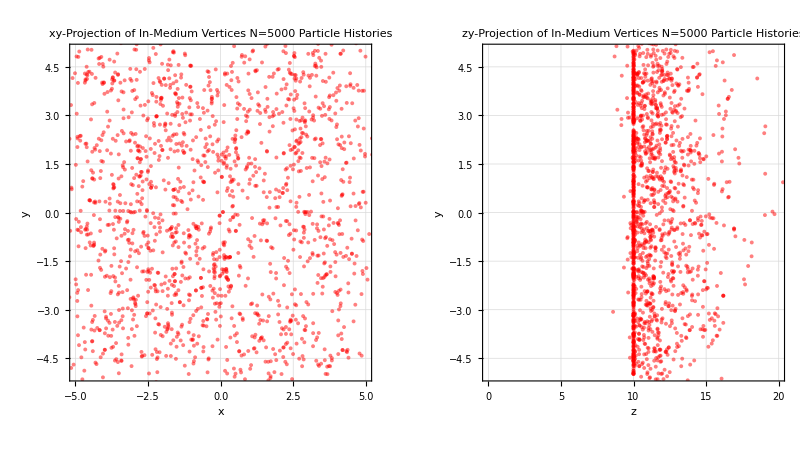

```mathematica
p1 = ListPlot[#[[1;;2]]&/@vertices, PlotRange->{{-a, a}/2, {-b, b}/2}, AxesLabel->{"x", "y"}, PlotStyle->{Red, Opacity[0.5], PointSize[0.007]}, Frame->True, AspectRatio->1, GridLines->Automatic, PlotLabel->"xy-Projection of In-Medium Vertices\n N=5000 Particle Histories",LabelStyle->Directive[Bold,Black], 
ImageSize->Full];
p2 = ListPlot[{#[[3]], #[[2]]}&/@vertices, PlotRange->{{0, c+z0}, {-b, b}/2}, AxesLabel->{"z", "y"}, PlotStyle->{Red, Opacity[0.5], PointSize[0.007]}, Frame->True, AspectRatio->1, GridLines->Automatic, PlotLabel->"zy-Projection of In-Medium Vertices\n N=5000 Particle Histories",LabelStyle->Directive[Bold,Black],
ImageSize->Full];
GraphicsRow[{p1, p2}, Background->LightBlue, Frame->True]

(*Export["ThankYouDavid.png",GraphicsRow[{p1, p2}, Background->LightBlue, Frame->True], ImageResolution->200]*)
```

```mathematica
(*Export["C:\\Users\\LNath\\OneDrive\\Documents\\University\\Science\\2024\\PHY3004W\\Project File\\Azimuthal_scattering_problem.png",%695,"PNG"];*)
```

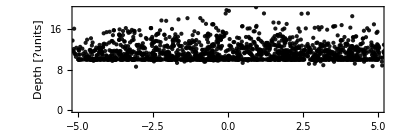

```mathematica
Graphics[{
Opacity[0.9],PointSize[Small],Point[#[[2;;3]]& /@vertices]},
Axes->{True, True},
AxesLabel->{"Distance [??units]", "Depth [?units]"},
AxesStyle->Dashed,
AxesOrigin->{0,0},
PlotRange->{{-b,b}/2,{0, c+z0}},
PlotRangeClipping->True,
Frame->True,
AspectRatio->1/3]
```

```mathematica
(*Export["C:\\Users\\LNath\\OneDrive\\Documents\\University\\Science\\2024\\PHY3004W\\Project File\\detector_scattering.png",%529,"PNG"];*)
```

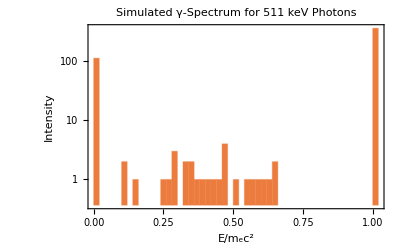

```mathematica
Histogram[energyDeposits, {0.02}, 
Frame->True,
PlotLabel->"Simulated γ-Spectrum for 511 keV Photons",
FrameLabel->{"E/m_ec^2", "Intensity"},
ScalingFunctions->"Log",(* PlotRange->{{0, 1}, {0,10}}*)
PlotTheme->"Scientific",
GridLines->{{1/3, 2/3}, Automatic}]
```

```mathematica
(*Export["C:\\Users\\LNath\\OneDrive\\Documents\\University\\Science\\2024\\PHY3004W\\Project File\\log_gamma_spectrum.png",%73,"PNG", ImageResolution->500];*)
```

```mathematica
(*Histogram[{#[[3]]&/@escapedForward, #[[3]]&/@escapedBackward}, {0.02}, 
Frame->True,
PlotLabel->"Photon Escape Energies",
ChartLegends->{"Forwad Escaped", "Backward Escaped"},
FrameLabel->{"E/m_ec^2", "Intensity"},
ScalingFunctions->"Log",(* PlotRange->{{0, 1}, {0,10}}*)
PlotTheme->"Scientific",
GridLines->{{1/3, 2/3}, Automatic}]*)
```

```mathematica
(*Export["C:\\Users\\LNath\\OneDrive\\Documents\\University\\Science\\2024\\PHY3004W\\Project File\\escape_energy_distribution.png",%716,"PNG"];*)
```

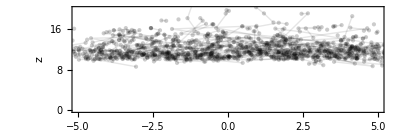

```mathematica
Graphics[{
Table[{
Opacity[0.1],Line[#[[2;;3]]&/@particleHistory[[2;;,1]]](*,Hue[RandomReal[]]*),
Opacity[0.2],Point[#[[2;;3]]&/@particleHistory[[2;;,1]]]},
{particleHistory,histories}]},
Axes->True,
AxesStyle->Dashed,
AxesLabel->{"y","z"},
AxesOrigin->{0,0},
PlotRangeClipping->True,
PlotRange->{{-b, b}/2,{0,c+z0}},
Frame->True,
AspectRatio->1/3]
```

```mathematica
(*Export["C:\\Users\\LNath\\OneDrive\\Documents\\University\\Science\\2024\\PHY3004W\\Project File\\detector_scattering_paths.png",%532,"PNG"];*)
```

### Escape distribution

```mathematica
(*(*#[[2]] &/@escapedForward*)
intersectDetector[{x_, y_, z_}, {θ_, ϕ_},flag_?BooleanQ]:=
Module[{𝕩, 𝕪, 𝕫,𝕥, t},
𝕩=Sin[θ] Cos[ϕ];
𝕪=Sin[θ] Sin[ϕ];
𝕫=Cos[θ];
If[flag, 𝕥 = ((L+ϵ)-z)/(𝕫-z),𝕥 = (-(L+ϵ)-z)/(𝕫-z)]; (*If flag is True, then intersect with backwards escape detector*)
(*substituting the intersection time t into the ray parametric equation*)
Return[{
x + t (𝕩-x),
y + t (𝕪-y), 
z + t (𝕫-z)}/. t->𝕥
];
];*)
```

```mathematica
(*forwardEscapeDetector = intersectDetector[#[[1]], #[[2]], True]&/@escapedForward;
backwardEscapeDetector = intersectDetector[#[[1]], #[[2]], False]&/@escapedBackward;*)
```

```mathematica
(*p3 = ListPlot[#[[1;;2]]&/@backwardEscapeDetector, PlotRange->{5 {-L, L}, 5{-L, L}}, AxesLabel->{"x", "y"}, PlotStyle->{Red, Opacity[0.7], PointSize[0.01]}, Frame->True, AspectRatio->1, GridLines->Automatic, PlotLabel->"Distribution of Backwards Escaped Particles\nN=5000 Particle Histories",LabelStyle->Directive[Bold,Black], 
ImageSize->Full];
p4 = ListPlot[#[[1;;2]]&/@forwardEscapeDetector, PlotRange->{5{-L, L}, 5{-L, L}}, AxesLabel->{"x", "y"}, PlotStyle->{Red, Opacity[0.7], PointSize[0.01]}, Frame->True, AspectRatio->1, GridLines->Automatic, PlotLabel->"Distribution of Forward Escaped Particles\nN=5000 Particle Histories",LabelStyle->Directive[Bold,Black], 
ImageSize->Full];
GraphicsRow[{p3, p4}, Background->LightBlue, Frame->True]*)
```

```mathematica
(**)
```

## Sim (Double Detector)

### Plots

## Spatial rESOLUTION

## tEMPORAL RESOLUTION

```mathematica
Real[ⅇ^(I θ)]
```

Real[ⅇ^(ⅈ θ)]